```mathematica
(*Makes func periodic*)
SetAttributes[periodic,HoldAll]
periodic[expr_,{s_Symbol,min_?NumberQ,max_?NumberQ}]:=Join[s&,With[{s:=Mod[s-min,max-min]+min},expr&]]

(*Li; initial grey level*)
(*Lf;  final grey level*)
tI =0.007;(*;  temporal delay*)
(*τ = 0.005 ; t90-t10 rise/fall times, get it from LUT*)
τs [τ_,Li_,Lf_]:=Piecewise[{{τ, Li==0 || Lf ==0}, {τ/(4 Log[3])Log[1+16/(1.8 Li/Lf+0.2)], True}}]
PWMLed[Modu_,Duty_,Hz_,t_]:=periodic[(1-Mod )+Mod* UnitBox[(Hz s)/(2 Duty)],{s,-1/Hz,1/Hz}][t]
Backlight[t_]:=PWMLed[1,0.7,500,t]
f[t_,τr_,τf_,Li_,Lf_]:=Backlight[t]*Piecewise[{{Li, Li==Lf}, {Li-(Li-Lf)/2(Tanh[(2 ArcTanh[0.8](t-tI))/τs[τf,Li,Lf]]+1), Li> Lf}, {Li+(Lf-Li)/2(Tanh[(2 ArcTanh[0.8](t-tI))/τs[τr,Li,Lf]]+1), Li<Lf}}]
Manipulate[Plot[f[t,0.004,0.005,i,o],{t,0,0.02},AxesOrigin->{0,0},PlotRange->{0,255},AxesLabel->{"Time","Grey level"},Filling->Bottom],{i,0,255},{o,0,255}]
```

```mathematica
InputType[Modu_,Duty_,Hz_,t_]:=UnitBox[(Hz t)/(2 Duty)]
Filter:=ButterworthFilterModel[{1,50}]
Filtered[Modu_,Duty_,Hz_,t_]:=OutputResponse[Filter,InputType[Mod,Duty,Hz,t],t]
InputType[1,0.7,500,t]
PWMLed[Modu_,Duty_,Hz_,t_]:=periodic[(1-Mod )+Mod* Filtered[Mod,Duty,Hz,s],{s,0/Hz,1/Hz}][t];
Plot[PWMLed[1,0.7,500,t],{t,0,0.1},PlotPoints->100];
Plot[Evaluate@OutputResponse[50/(50+s),PWMLed[1,0.7,500,t],t],{t,0,0.1}];
```

UnitBox[357.143 t]

{50 (Piecewise[{{1/50 ⅇ^(-25-50 t) (1-ⅇ^25), t≤-1/2}, {1/50 ⅇ^(-50 t) (-1+ⅇ^(50 t)), -1/2<t≤1/2}, {1/50 ⅇ^(-50 t) (-1+ⅇ^25), True}}])}

```mathematica
InputType[Modu_,Duty_,Hz_,t_]:=UnitBox[(Hz t)/(2 Duty)]
InputType[1,0.7,500,t]
(*Filter:=ButterworthFilterModel[{1,50}]
Filtered[Modu_,Duty_,Hz_,t_]:=Evaluate@OutputResponse[Filter,InputType[Mod,Duty,Hz,t],t]
Filtered[1,0.7,500,t]//Quiet
Plot[Evaluate@Filtered[1,0.7,500,t],{t,0,0.01}]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

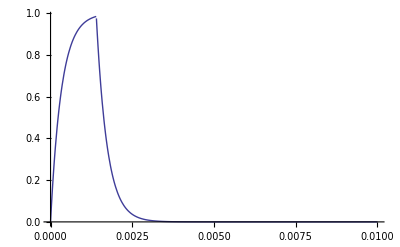

OutputResponse::nsymb: 2.04286×10^-7 must be a symbol.

OutputResponse::nsymb: 0.000204286 must be a symbol.

General::stop: Further output of OutputResponse :: nsymb will be suppressed during this calculation.

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

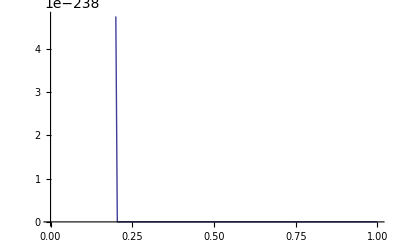

```mathematica
InputType[Modu_,Duty_,Hz_,t_]:=UnitBox[(Hz t)/(2 Duty)]
Filter:=ButterworthFilterModel[{1,3000}]
Filtered[Modu_,Duty_,Hz_,t_]:=OutputResponse[Filter,InputType[Mod,Duty,Hz,t],t]
Plot[Evaluate@Filtered[1,0.7,500,t],{t,0,0.01},PlotRange->Full]
Plot[PWMLed[1,0.7,500,t],{t,0,0.01},PlotRange->Full];
Plot[periodic[Evaluate@Filtered[1,0.7,500,s],{s,0,1}][t],{t,0,1}]
(*PWMLed[Modu_,Duty_,Hz_,t_]:=periodic[(1-Mod )+Mod* Filtered[Mod,Duty,Hz,s],{s,0/Hz,1/Hz}][t];*)
```

```mathematica
SamplingPeriod
```